```mathematica
A=({{1, 0, -1, 0, 0, 0, -1, 0, 0, 0}, {0, -1, 0, -1, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, -1, 0, 0, -1, 0, 0}, {0, 0, 0, 1, 0, -1, 0, 1, 0, 0}, {-R1, 0, -s*C1, 0, -s*C3, 0, 0, 0, 1, 0}, {0, 0, s*C1, -s*C2, 0, 0, -s*C5, s*C6, 0, 0}, {0, 0, 0, 0, s*C3, -s*C4, 0, -s*C6, 0, 0}, {0, -R2, 0, s*C2, 0, s*C4, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, -R2, 0, 0, 0, 0, 0, 0, 0, 1}});B=({{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {2}, {0}});
```

```mathematica
R1=1;R2=1;C1=1;C2=2;C3=3;C4=4;C5=5;C6=6;
```

```mathematica
LinearSolve[A,B]
```

{{(4 (73+252 s))/(146+913 s+970 s^2)},{(508 s)/(146+913 s+970 s^2)},{(10 (23+62 s))/(146+913 s+970 s^2)},{-(2 (-31+60 s))/(146+913 s+970 s^2)},{(4 (49+110 s))/(146+913 s+970 s^2)},{(12 (8+5 s))/(146+913 s+970 s^2)},{(2 (31+194 s))/(146+913 s+970 s^2)},{(2 (17+90 s))/(146+913 s+970 s^2)},{2},{(508 s)/(146+913 s+970 s^2)}}

```mathematica
salida[t_]=InverseLaplaceTransform[(254 s)/(146+913 s+970 s^2),s,t]
```

```mathematica
1/(970 √267089)127 (913 ⅇ^((-913/1940-(√267089)/1940) t)+√267089 ⅇ^((-913/1940-(√267089)/1940) t)-913 ⅇ^((-913/1940+(√267089)/1940) t)+√267089 ⅇ^((-913/1940+(√267089)/1940) t))
FullSimplify[salida]
```

1/(970 √267089)127 (913 ⅇ^((-913/1940-(√267089)/1940) t)+√267089 ⅇ^((-913/1940-(√267089)/1940) t)-913 ⅇ^((-913/1940+(√267089)/1940) t)+√267089 ⅇ^((-913/1940+(√267089)/1940) t))

salida

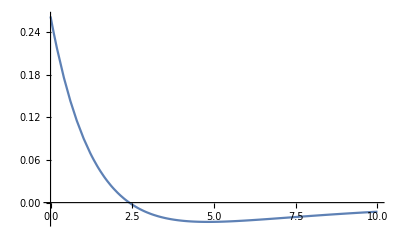

```mathematica
Plot[salida[t],{t,0,10},PlotRange->All]
```

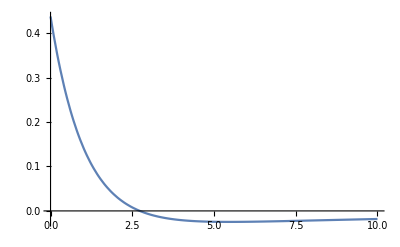

```mathematica
Plot[0.4813*Exp[-0.9645*t]-0.0440*Exp[-0.0882*t],{t,0,10},PlotRange->All]
```

```mathematica
LaplaceTransform[0.4813*Exp[-0.9645*t]-0.0440*Exp[-0.0882*t],t,s]
```

-0.044/(0.0882+s)+0.4813/(0.9645+s)

```mathematica
[-0.044/(0.0882+s)+0.4813/(0.9645+s)]
```

Plus[Times[-0.044,Power[Plus[0.0882,s],-1]],Times[0.4813,Power[Plus[0.9645,s],-1]]]